```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]] ;
```

This Mathematica code is part of the lecture script Introduction to Computational Quantum Mechanics by Roman Schmied. It is licensed under a Creative Commons Attribution-ShareAlike 4.0 International License.

-Graphics-

You can download the associated lecture script at http://arxiv.org/abs/1403.7050

# quantum-mechanical spin and angular momentum operators

```mathematica
SpinQ[S_]:=IntegerQ[2S]&&S≥0
splus[0]={{0}}//SparseArray;
splus[S_?SpinQ]:=splus[S]= SparseArray[Band[{1,2}]->Table[Sqrt[S(S+1)-M(M+1)],{M,S-1,-S,-1}],{2S+1,2S+1}]
sminus[S_?SpinQ]:=Transpose[splus[S]]
sx[S_?SpinQ]:=sx[S]=(splus[S]+sminus[S])/2
sy[S_?SpinQ]:=sy[S]=(splus[S]-sminus[S])/(2I)
sz[S_?SpinQ]:=sz[S]=SparseArray[Band[{1,1}]->Range[S,-S,-1],{2S+1,2S+1}]
id[S_?SpinQ]:=id[S]=IdentityMatrix[2S+1,SparseArray]
```

### operators acting on many spins

an operator a acting on spin k out of a set of n spins-S:

```mathematica
op[S_?SpinQ,n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2S+1,2S+1}:=KroneckerProduct[IdentityMatrix[(2S+1)^(k-1),SparseArray],a,IdentityMatrix[(2S+1)^(n-k),SparseArray]]
```

spin operators acting on spin k out of a set of n spins-S:

```mathematica
Sx[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sx[S]]
Sy[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sy[S]]
Sz[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sz[S]]
Sp[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,splus[S]]
Sm[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sminus[S]]
Id[S_?SpinQ,n_Integer]:=IdentityMatrix[(2S+1)^n,SparseArray]
```

Operadores atuando sobre mais de um spin

```mathematica
SS[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤(n-1):=Sx[S,n,k].Sx[S,n,k+1]+Sy[S,n,k].Sy[S,n,k+1]+Sz[S,n,k].Sz[S,n,k+1] (* Produto escalar de dois spins vizinhos *)
ST2[S_?SpinQ,n_Integer]:=(Sum[Sx[S,n,k],{k,1,n}]).(Sum[Sx[S,n,k],{k,1,n}])+(Sum[Sy[S,n,k],{k,1,n}]).(Sum[Sy[S,n,k],{k,1,n}])+(Sum[Sz[S,n,k],{k,1,n}]).(Sum[Sz[S,n,k],{k,1,n}]) (* Quadrado do spin total *)
STz[S_?SpinQ,n_Integer]:=Sum[Sz[S,n,k],{k,1,n}] (* Componente z do spin total *)
```

Tensores esfericamente irredutíveis

```mathematica
Subscript[Y, 0,0][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=1/Sqrt[4*Pi]*Id[S,n]
Subscript[Y, 1,0][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[3/(4*Pi)]*Sz[S,n,k]
Subscript[Y, 1,1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=-Sqrt[3/(8*Pi)]*Sp[S,n,k]
Subscript[Y, 1,-1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[3/(8*Pi)]*Sm[S,n,k]
Subscript[Y, 2,0][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=-Sqrt[5/(16*Pi)]*(S*(S+1)*Id[S,n]-3*Sz[S,n,k].Sz[S,n,k])
Subscript[Y, 2,1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=-Sqrt[15/(32*Pi)]*(Sz[S,n,k].Sp[S,n,k]+Sp[S,n,k].Sz[S,n,k])
Subscript[Y, 2,-1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[15/(32*Pi)]*(Sz[S,n,k].Sm[S,n,k]+Sm[S,n,k].Sz[S,n,k])
Subscript[Y, 2,2][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[15/(32*Pi)]*Sp[S,n,k].Sp[S,n,k]
Subscript[Y, 2,-2][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[15/(32*Pi)]*Sm[S,n,k].Sm[S,n,k]
```

Operadores O definidos na equação (4.11) da tese do Victor Quito; note o uso da letra OJ para representar o operador no Mathematica, uma vez que O é uma variável reservada.

```mathematica
NonNegativeQ[J_]:=IntegerQ[J]&&J≥0
OJ[J_?NonNegativeQ,S_?SpinQ,n_Integer,k_Integer]/;1≤ k≤(n-1):=Sum[(-1)^M*Subscript[Y, J,-M][S,n,k].Subscript[Y, J,M][S,n,k+1],{M,-J,J}]
```

### Operadores para um sítio S misto

```mathematica
Operador[sitios_,sitiooperador_,operador_]:={
esquerda=If[sitiooperador>1,Product[2 sitios[[i]]+ 1,{i,1,sitiooperador-1}],0];
direita=If[sitiooperador<Dimensions[sitios][[1]],Product[2 sitios[[i]]+ 1,{i,sitiooperador+1,Dimensions[sitios][[1]]}],0];
If[esquerda>0,nop=KroneckerProduct[IdentityMatrix[esquerda,SparseArray],operador],nop=operador];
If[direita>0,nop=KroneckerProduct[nop,IdentityMatrix[direita,SparseArray]]];
nop}
```

```mathematica
OJg[J_?NonNegativeQ,sitios_,sitiooperador_]:=Sum[(-1)^M*(Operador[sitios,sitiooperador,Subscript[Y, J,-M][sitios[[sitiooperador]],1,1]][[1]]).(Operador[sitios,sitiooperador+1,Subscript[Y, J,M][sitios[[sitiooperador+1]],1,1]][[1]]),{M,-J,J}]  (*Operador OJ *)
OJ2v[J_?NonNegativeQ,sitios_,sitiooperador_]:=Sum[(-1)^M*(Operador[sitios,sitiooperador,Subscript[Y, J,-M][sitios[[sitiooperador]],1,1]][[1]]).(Operador[sitios,sitiooperador+2,Subscript[Y, J,M][sitios[[sitiooperador+2]],1,1]][[1]]),{M,-J,J}] (*Operador OJ para segundos vizinhos *)
```

```mathematica
STzg[sitios_]:=Sum[Operador[sitios,k,Sz[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]  (*Sz do spin total*)
STpg[sitios_]:=Sum[Operador[sitios,k,Sp[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]  (*Sp do spin total*)
STmg[sitios_]:=Sum[Operador[sitios,k,Sm[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]  (*Sp do spin total*)
```

```mathematica
ST2g[sitios_]:=(Sum[Operador[sitios,k,Sx[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]).(Sum[Operador[sitios,k,Sx[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}])+(Sum[Operador[sitios,k,Sy[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]).(Sum[Operador[sitios,k,Sy[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}])+(Sum[Operador[sitios,k,Sz[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]).(Sum[Operador[sitios,k,Sz[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]) (* Quadrado do spin total*)
```

```mathematica
Yg[sitios_,sitiooperador_,J_,M_]:=Operador[sitios,sitiooperador,Subscript[Y, J,-M][sitios[[sitiooperador]],1,1]][[1]] (* Operadores Y fornecendo o sítio*)
```

# Funções de mapeamento e renormalização

## Funções úteis

```mathematica
KtoJ[k1_,k2_]:=(1/(16π))(12k1+15k2)//Simplify
KtoD[k2_]:=(15/(8π))k2//Simplify
KtoJD[k1_,k2_]:={KtoJ[k1,k2],KtoD[k2]}//Simplify
KtoJD::usage="KtoJD[K_1, K_2] converte os valores de {K_1, K_2} -> {J, D}";
```

```mathematica
JtoK1[j_,d_]:=4π j/3 - 2π d/3 //Simplify
DtoK2[d_]:=8π d/15//Simplify
JDtoK[j_,d_]:={JtoK1[j,d],DtoK2[d]}//Simplify
JDtoK::usage="JDtoK[J, D] converte os valores de {J, D} -> {K_1, K_2}";
```

```mathematica
AngJD[j_,d_]:=Module[{θ},If[d≠0&&Abs[j/d]<10^-10,θ=If[d>0,90,-90],θ=If[j≠0,If[j>0,(180 ArcTan[d/j])/π,(180 ArcTan[d/j])/π+180],If[d>0,90,If[d<0,-90,0]]];If[θ>180,θ=θ-360];θ]]
AngJD::usage="AngJD[J, D] retorna o angulo entre os valores J e D em graus";
```

```mathematica
AngK[k1_,k2_]:=Module[{θ,j,d},{j,d}=N[KtoJD[k1,k2]];AngJD[j,d]]
AngK::usage="AngK[K_1, K_2] retorna o angulo entre os coeficientes K em graus";
```

```mathematica
Num63[n_]:=(Total[MatrixPower[{{4, 2}, {2, 1}},n].{0, 1}])
Num63::usage="Num63[n] retorna o número n de elementos para uma cadeia 63";
```

## Função que criam um H

### Hamiltoniano

A entrada dos sítios é {S_1,S_2... S_n} e {k_1, k_2}

```mathematica
H[sitios_,k_]:=Module[{J,n},Sum[Sum[k[[J]]*OJg[J,sitios,n],{J,1,2}],{n,1,Dimensions[sitios][[1]]-1}]]
```

### Criar Hamiltoniano com base cadeia

É preciso fornecer os valores individuais dos spins e dos k_a e k_b para cada ligação, um exemplo cadeia={{k_a_1,k_a_2,S_1,1},{k_b_1,k_b_2,S_2,2},{k_a_1,k_a_2,S_3,3},{0,0,S_4,4}}

```mathematica
Hcadeia[array_]:=(
	Module[{cadeiahcad,k,s,h,kn,i},
	k=array[[All,1;;2]];
	s=array[[All,3]];
	i=1;
	While[i<Dimensions[s][[1]],
		kn[1]=k[[i,1]];
		kn[2]=k[[i,2]];
		h[i]=Sum[kn[J]*OJg[J,s,i],{J,1,2}];
		i=i+1;];
h=Sum[h[n],{n,1,Dimensions[s][[1]]-1}];
h])
```

## Funções de calculo dos coeficientes de primeira ou segunda ordem

### Coeficientes G

```mathematica
Gj[sitio_,vecs_,J_,M_,min_,dim_,k_]:=2Sum[If[i==min,0,(vecs[[min]].Yg[sitio,1,J,-M].vecs[[i]])(vecs[[i]].Yg[sitio,Dimensions[sitio][[1]],J,M].vecs[[min]])/(vecs[[min]].H[sitio,k].vecs[[min]]-vecs[[i]].H[sitio,k].vecs[[i]])],{i,1,dim}]//Simplify
```

### Coeficientes F

```mathematica
fj[sitio_,vetor_,sitiooperando_,J_,S_]:=If[(S==1/2&&J==2),0,N[Round[vetor.Yg[sitio,sitiooperando,J,0].vetor/determinantefj[S,J],10^-12]]]
```

```mathematica
determinantefj[S_,J_]:=(Module[{dim,vec},
dim=Round[2S];
vec={1};
Do[vec=Insert[vec,0,-1],dim];
vec.Subscript[Y, J,0][S,1,1].vec])
```

## Função para encontrar o gap

Caso o GAP seja menor doq 10^-12 a função precisa ser reajustada.
Ajustar o critério do calculo do gap em relação ao valor do acoplamento

```mathematica
calgap[Mgap_]:=(
Module[{H,norm,en},
norm=Max[Abs[Mgap]];
H=N[Mgap]/norm;
en=DeleteDuplicates[N[Sort[Round[Sort[Eigenvalues[H]], 10^-8]]]];
If[Dimensions[en][[1]]>1,norm*(en[[2]]-en[[1]]),0]])
```

```mathematica
gapcad[array_]:=calgap[Hcadeia[array]]
```

```mathematica
GapN[Mgap_,n_]:=(
Module[{Hgap,normgap,egap,gapc},
Hgap=N[Mgap];
egap=Sort[Eigenvalues[Hgap]];
egap=DeleteDuplicates[N[Sort[Round[egap, 10^-12]]]];
gapc=(egap[[n]]-egap[[1]])])
```

## Criação Cadeia De Fibonacci

```mathematica
Cadeiafibonacci[m_,kb1_,kb2_,razao_]:=(
Module[{ifb,kb1fb,kb2fb,ka1fb,ka2fb,jfb,lfb,cadeia,st},
Clear[cadeia];
Clear[st];
ifb=m;
kb1fb=kb1;
kb2fb=kb2;
ka1fb=kb1fb/razao;
ka2fb=kb2fb/razao;
jfb=2;
lfb=2;
cadeia=Array[st,ifb+1];(* Criando um vetor que guarda os tipos de ligação*)
st[1]={ka1fb,ka2fb,1, 1,1};
st[2]={kb1fb,kb2fb,1, 2,2};
If[kb1≠0,
While[lfb≤ifb,{If[st[jfb][[1]]==ka1fb,{st[lfb+1]={ka1fb,ka2fb,1,lfb+1,lfb+1},st[lfb+2]={kb1fb,kb2fb,1,lfb+2,lfb+2},lfb=lfb+2,jfb=jfb+1}];
If[st[jfb][[1]]==kb1fb,{st[lfb+1]={ka1fb,ka2fb,1, lfb+1, lfb+1},lfb=lfb+1,jfb=jfb+1}]};](*a->ab b->a*);
st[m+1]={0.,0.,1, m+1,m+1},

While[lfb≤ifb,{If[st[jfb][[2]]==ka2fb,{st[lfb+1]={ka1fb,ka2fb,1,lfb+1,lfb+1},st[lfb+2]={kb1fb,kb2fb,1,lfb+2,lfb+2},lfb=lfb+2,jfb=jfb+1}];
If[st[jfb][[2]]==kb2fb,{st[lfb+1]={ka1fb,ka2fb,1, lfb+1, lfb+1},lfb=lfb+1,jfb=jfb+1}]};](*a->ab b->a*);
st[m+1]={0.,0.,1, m+1,m+1}];
cadeia]
)
```

```mathematica
Cadeiafibonaccimeio[m_,kb1_,kb2_,razao_]:=(
Module[{ifb,kb1fb,kb2fb,ka1fb,ka2fb,jfb,lfb,cadeia,st},
Clear[cadeia];
Clear[st];
ifb=m;
kb1fb=kb1;
kb2fb=kb2;
ka1fb=kb1fb/razao;
ka2fb=kb2fb/razao;
jfb=2;
lfb=2;
cadeia=Array[st,ifb+1];(* Criando um vetor que guarda os tipos de ligação*)
st[1]={ka1fb,ka2fb,1/2, 1,1};
st[2]={kb1fb,kb2fb,1/2, 2,2};
If[kb1≠0,
While[lfb≤ifb,{If[st[jfb][[1]]==ka1fb,{st[lfb+1]={ka1fb,ka2fb,1/2,lfb+1,lfb+1},st[lfb+2]={kb1fb,kb2fb,1/2,lfb+2,lfb+2},lfb=lfb+2,jfb=jfb+1}];
If[st[jfb][[1]]==kb1fb,{st[lfb+1]={ka1fb,ka2fb,1/2, lfb+1, lfb+1},lfb=lfb+1,jfb=jfb+1}]};](*a->ab b->a*);
st[m+1]={0.,0.,1/2, m+1,m+1},

While[lfb≤ifb,{If[st[jfb][[2]]==ka2fb,{st[lfb+1]={ka1fb,ka2fb,1/2,lfb+1,lfb+1},st[lfb+2]={kb1fb,kb2fb,1/2,lfb+2,lfb+2},lfb=lfb+2,jfb=jfb+1}];
If[st[jfb][[2]]==kb2fb,{st[lfb+1]={ka1fb,ka2fb,1/2, lfb+1, lfb+1},lfb=lfb+1,jfb=jfb+1}]};](*a->ab b->a*);
st[m+1]={0.,0.,1/2, m+1,m+1}];
cadeia]
)
```

```mathematica
Cadeia36[m_,kb1_,kb2_,razao_]:=(
Module[{ifb,kb1fb,kb2fb,ka1fb,ka2fb,jfb,lfb,cadeia,st},
Clear[cadeia];
Clear[st];
ifb=m;
kb1fb=kb1;
kb2fb=kb2;
ka1fb=kb1fb/razao;
ka2fb=kb2fb/razao;
jfb=2;
lfb=3;
cadeia=Array[st,ifb+1];(* Criando um vetor que guarda os tipos de ligação*)
st[1]={kb1fb,kb2fb,1, 1,1};
st[2]={ka1fb,ka2fb,1, 2,2};
st[3]={ka1fb,ka2fb,1, 2,3};
If[kb1≠0,
While[lfb≤ifb,{If[st[jfb][[1]]==ka1fb,{
st[lfb+1]={kb1fb,kb2fb,1,lfb+1,lfb+1},
st[lfb+2]={ka1fb,ka2fb,1,lfb+2,lfb+2},
st[lfb+3]={kb1fb,kb2fb,1,lfb+3,lfb+3},
st[lfb+4]={ka1fb,ka2fb,1,lfb+4,lfb+4},
st[lfb+5]={ka1fb,ka2fb,1,lfb+5,lfb+5},
st[lfb+6]={ka1fb,ka2fb,1,lfb+6,lfb+6},
lfb=lfb+6,
jfb=jfb+1
}];
If[st[jfb][[1]]==kb1fb,{
st[lfb+1]={kb1fb,kb2fb,1, lfb+1, lfb+1},
st[lfb+2]={ka1fb,ka2fb,1, lfb+2, lfb+2},
st[lfb+3]={ka1fb,ka2fb,1, lfb+3, lfb+3},
lfb=lfb+3,
jfb=jfb+1
}]};](*a->babaaa b->baa*);
st[m+1]={0.,0.,1, m+1,m+1},

While[lfb≤ifb,{If[st[jfb][[2]]==ka2fb,{st[lfb+1]={ka1fb,ka2fb,1,lfb+1,lfb+1},st[lfb+2]={kb1fb,kb2fb,1,lfb+2,lfb+2},lfb=lfb+2,jfb=jfb+1}];
If[st[jfb][[2]]==kb2fb,{st[lfb+1]={ka1fb,ka2fb,1, lfb+1, lfb+1},lfb=lfb+1,jfb=jfb+1}]};](*a->ab b->a*);
st[m+1]={0.,0.,1, m+1,m+1}];
cadeia]
)
```

## Identificar blocos únicos

```mathematica
blocounico[array_]:=(
Module[{k,j,blocos,Kn,blocon,linha,contagem},
k=0;
j=1;
blocos={};
contagem={};
While[j<Dimensions[array][[1]],
	Kn={array[[j]][[1]],array[[j]][[2]]};
	blocon={array[[j]][[3]]};
	While[Kn=={array[[j]][[1]],array[[j]][[2]]}&&j<Length[array],
	blocon=Insert[blocon,array[[j+1]][[3]],-1];
j=j+1;
];
linha={Kn,blocon};
If[Not[MemberQ[blocos,linha]],{blocos=Insert[blocos,linha,-1],contagem=Insert[contagem,1,-1]},
contagem[[Flatten[Position[blocos,linha][[1]]]]]=contagem[[Flatten[Position[blocos,linha][[1]]]]]+1
];
];
{blocos,contagem}])
```

## Calcular Gap e S’ dos blocos únicos

```mathematica
Gapblocounico[array_]:=(
Module[{bloco,razgapvizinho,K1,pnl,jb,db,razao,ja,da,Gapspinbu,jgapbu,k,Hgapunico,maxhpunico,energiabu,minvecgu,Sgu,gabc,θi,max,contagem},
{bloco,contagem}=blocounico[array];
Gapspinbu={};
jgapbu=1;
K1=array[[1;;Dimensions[array][[1]]-1,1;;2]];
While[jgapbu<=Dimensions[bloco][[1]],
	k[1]=bloco[[jgapbu]][[1]][[1]];
	k[2]=bloco[[jgapbu]][[1]][[2]];
	Hgapunico=H[bloco[[jgapbu]][[2]],{k[1],k[2]}];
	gabc=calgap[Hgapunico];
	Gapspinbu=Insert[Gapspinbu,{gabc},-1];
	jgapbu++];
pnl=Position[Gapspinbu,Max[Gapspinbu[[All,1]]]][[1,1]];
{jb,db}=KtoJD[bloco[[pnl,1,1]],bloco[[pnl,1,2]]];
jgapbu=1;
razao={};
While[jgapbu<=Dimensions[bloco][[1]],
{ja,da}=KtoJD[bloco[[jgapbu,1,1]],bloco[[jgapbu,1,2]]];
θi=AngJD[ja,da];
	razao=Insert[razao,{ja,da,Gapspinbu[[jgapbu,1]],Abs[RazJD[ja,jb]],Abs[RazJD[da,db]],θi,Count[K1,{bloco[[jgapbu,1,1]],bloco[[jgapbu,1,2]]}]},-1];
	jgapbu++];
max=Position[Gapspinbu,Max[Gapspinbu]][[1,1]];
razgapvizinho=GapVizinho[array,bloco[[max,1]],bloco[[max,2]],Gapspinbu[[max]][[1]]];
{Gapspinbu,bloco,razao,razgapvizinho,contagem[[max]]}
])
```

```mathematica
GapVizinho[array_,k_,spins_,gap_]:=(
Module[{inicio,final,j,GBU,K,blocobu,linhabu,θi},
GBU={};
j=1;
While[j<Dimensions[array][[1]]&&Dimensions[GBU][[1]]<100,
K={array[[j]][[1]],array[[j]][[2]]};
If[K==k,
	inicio=j;
	blocobu={array[[j,3]]};
	While[K=={array[[j,1]],array[[j,2]]}&&j<Dimensions[array][[1]],
	blocobu=Insert[blocobu,array[[j+1]][[3]],-1];
	j++;];
final=j;
linhabu={inicio,final,BlocoVizionhoEsquerdo[array,inicio]/gap,BlocoVizionhoDireita[array,final]/gap,AngVizinhoEsquerda[array,inicio],AngVizinhoDireita[array,final]};
If[blocobu==spins&&k==K,GBU=Insert[GBU,linhabu,-1]];
];
j=j+1;
];
GBU])
```

```mathematica
BlocoVizionhoDireita[cad_,j_]:=Module[{k,i,l,Ja,Da,S},k=cad⟦j,1;;2⟧;If[k!={0,0},i=j;l=j;S={cad⟦j,3⟧};While[cad⟦i⟧⟦1;;2⟧==k&&i<Dimensions[cad][[1]],{S=Insert[S,cad⟦l+1,3⟧,-1],l++,i++}];
calgap[H[S,k]],0]]
```

```mathematica
BlocoVizionhoEsquerdo[cad_,j_]:=Module[{k,i,l,S},If[j>1,k=cad⟦j-1,1;;2⟧;i=j-1;l=j;S={cad⟦j,3⟧};While[i≥1&&cad⟦i,1;;2⟧==k,{S=Insert[S,cad⟦i,3⟧,1],i--}];If[Dimensions[S]⟦1⟧>1,calgap[H[S,k]],0],0]]
```

```mathematica
AngVizinhoDireita[cad_,j_]:=Module[{k,i,l,Ja,Da,S},k=cad⟦j,1;;2⟧;If[k!={0,0},i=j;l=j;S={cad⟦j,3⟧};While[cad⟦i⟧⟦1;;2⟧==k&&i<Dimensions[cad][[1]],{S=Insert[S,cad⟦l+1,3⟧,-1],l++,i++}];
{Ja,Da}={KtoJ[k[[1]],k[[2]]],KtoD[k[[2]]]};
AngJD[Ja,Da],0]]
```

```mathematica
AngVizinhoEsquerda[cad_,j_]:=Module[{k,i,l,Ja,Da,S},If[j>1,k=cad⟦j-1,1;;2⟧;i=j-1;l=j-1;S={cad⟦j,3⟧};While[i≥1&&cad⟦i,1;;2⟧==k,{S=Insert[S,cad⟦i,3⟧,1],i--}];{Ja,Da}=KtoJD[k[[1]],k[[2]]];If[Dimensions[S]⟦1⟧>1,AngJD[Ja,Da],0],0]]
```

## Calculando as novas ligações

```mathematica
novaligacao[cad_]:=(
Module[{Lig,gapvizinho,Gnl,razao,Anl,pnl,Stil,vals,vecs,minvecnl,stznl,GNL,k,minnl,vecsanl,dimnl,bloconl,min,ListaS,contagem},
Lig=Gapblocounico[cad];
{Gnl,Anl,razao,gapvizinho,contagem}=Lig;
pnl=Position[Gnl,Max[Gnl[[All,1]]]][[1,1]];
{vals,vecs,minvecnl,min}=Vetormin[Anl[[pnl,2]],Anl[[pnl,1]]];
ListaS=calcS[vecs,Anl[[pnl,2]],min];
Stil=minvecnl.ST2g[Anl[[pnl,2]]].minvecnl;
Stil=Round[-0.5+0.5 Sqrt[1+4Stil],1/2];
If[Stil>0,
	stznl=Round[minvecnl.STzg[Anl[[pnl,2]]].minvecnl,1/2];
	GNL={Anl[[pnl]][[1]],Anl[[pnl]][[2]],{fj[Anl[[pnl,2]],minvecnl,1,1,Stil],fj[Anl[[pnl,2]],minvecnl,1,2,Stil],fj[Anl[[pnl,2]],minvecnl,Length[Anl[[pnl]][[2]]],1,Stil],fj[Anl[[pnl,2]],minvecnl,Length[Anl[[pnl]][[2]]],2,Stil]},{Stil,stznl}}
];
If[Stil==0,
	k[1]=Anl[[pnl]][[1]][[1]];
	k[2]=Anl[[pnl]][[1]][[2]];
	minnl=minnl=Flatten[Position[vals,Min[vals]]][[1]];
	dimnl=Dimensions[vecs][[1]];
	bloconl=Anl[[pnl,2]];
	GNL={Anl[[pnl]][[1]],Anl[[pnl]][[2]],{Gj[bloconl,vecs,1,0,minnl,dimnl,{k[1],k[2]}],Gj[bloconl,vecs,2,0,minnl,dimnl,{k[1],k[2]}]},{Stil}};
];
{GNL,Lig,ListaS,gapvizinho,contagem}])
```

```mathematica
calcS[vec_,spin_,min_]:=(Module[{j,S},
S={};

For[j=1,j<=Dimensions[min][[1]],j++,S=Insert[S,Round[vec[[min[[j]]]].ST2g[spin].vec[[min[[j]]]]],-1]];
S])
```

## Auto vetores e o auto vetor associado ao menor auto valor com máximo de Sz

Achar o vetor com Sz >0 associado ao menor auto valor é necessário para calcular o valor de F

```mathematica
Vetormin[spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,Stil,i, Hvetormin, rescale},
i=2;
{vals,vecs,vecmin,sz1,min}=metodo[1][spins,k/Max[Abs[k]]];
Stil=vecmin.ST2g[spins].vecmin;
Stil=Round[-0.5+0.5 Sqrt[1+4Stil],1/2];
While[Abs[sz1-Stil]>0.001&&i<=10,{{vals,vecs,vecmin,sz1,min}=metodo[i][spins,k/Max[Abs[k]]],i++}];
{vals,vecs,vecmin,min}])
```

#### Metodo normal

```mathematica
metodo[1][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = H[spins,k];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[2][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = H[spins,k];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo Banded

```mathematica
metodo[3][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = H[spins,k];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[4][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = H[spins,k];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo SetPrecision32

```mathematica
metodo[5][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[H[spins,k],32];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[6][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ H[spins,k],32];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo SetPrecision64

```mathematica
metodo[7][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[H[spins,k],64];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[8][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ H[spins,k],64];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo SetPrecision128

```mathematica
metodo[9][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[H[spins,k],128];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[10][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ H[spins,k],128];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

## S final cadeia

```mathematica
Stotalcad[array_]:=(Module[{vals,vecs,min,vecmin,sz1,Stil,i, Hvetormin, rescale,x},
x=array;
x[[All,1]]=array[[All,1]]/Max[Abs[array[[All,1;;2]]]];
x[[All,2]] = array[[All,2]]/Max[Abs[array[[All,1;;2]]]];
i=2;
{vals,vecs,vecmin,sz1}=metodoStotalcad[1][x];
Stil=vecmin.ST2g[x[[All,3]]].vecmin;
Stil=Round[-0.5+0.5 Sqrt[1+4Stil],1/2];
While[Abs[sz1-Stil]>0.001&&i<=10,{{vals,vecs,vecmin,sz1}=metodoStotalcad[i][x],i++}];
vecmin.ST2g[x[[All,3]]].vecmin])
```

#### Metodo normal

```mathematica
metodoStotalcad[1][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = Hcadeia[array];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[2][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = Hcadeia[array];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo Banded

```mathematica
metodoStotalcad[3][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin =  Hcadeia[array];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[4][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = Hcadeia[array];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo SetPrecision32

```mathematica
metodoStotalcad[5][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[Hcadeia[array],32];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[6][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ Hcadeia[array],32];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo SetPrecision64

```mathematica
metodoStotalcad[7][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[Hcadeia[array],64];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[8][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ Hcadeia[array],64];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo SetPrecision128

```mathematica
metodoStotalcad[9][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[Hcadeia[array],128];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[10][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ Hcadeia[array],128];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

## Renormalização

### Renormalizar bloco S’>0

```mathematica
ren1[cadeia1_,inicialren_,finalren_, Fs_, Stil_]:=(
Module[{cadeiaren1,inicalren1,finalrean1,iren1,Fren1},
cadeiaren1=cadeia1;
inicalren1=inicialren;
finalrean1=finalren;
iren1=0;
Fren1=Fs;
If[inicialren>1 ,{
cadeiaren1[[inicalren1-1]]={cadeiaren1[[inicalren1-1,1]] Fren1[[1]],cadeiaren1[[inicalren1-1,2]] Fren1[[2]],cadeiaren1[[inicalren1-1,3]],cadeiaren1[[inicalren1-1,4]],cadeiaren1[[inicalren1-1,5]]};
cadeiaren1[[finalrean1]]={cadeiaren1[[finalrean1,1]] Fren1[[3]],cadeiaren1[[finalrean1,2]] Fren1[[4]],Stil,cadeiaren1[[finalrean1,4]],cadeiaren1[[finalrean1,5]]};
While[(inicalren1+iren1)<(finalrean1),cadeiaren1[[(inicalren1+iren1)]]={0};iren1++]}];
If[inicialren==1,{
cadeiaren1[[finalrean1]]={cadeiaren1[[finalrean1,1]] Fren1[[3]],cadeiaren1[[finalrean1,2]] Fren1[[4]],Stil,cadeiaren1[[finalrean1,4]],cadeiaren1[[finalrean1,5]]};
While[(inicalren1+iren1)<finalrean1,cadeiaren1[[(inicalren1+iren1)]]={0};iren1++]}];
DeleteCases[cadeiaren1,{0}]])
```

### Renormalizar bloco S’=0

```mathematica
ren0[cadeia1_,inicialren_,finalren_, Gs_]:=(
Module[{cadeiaren0,inicalren0,finalrean0,iren0,Gren0},
cadeiaren0=cadeia1;
inicalren0=inicialren;
finalrean0=finalren;
iren0=0;
Gren0=Gs;
If[inicalren0>1,{cadeiaren0[[inicalren0-1]]={cadeiaren0[[inicalren0-1,1]]cadeiaren0[[finalrean0,1]] Gren0[[1]],cadeiaren0[[inicalren0-1,2]]cadeiaren0[[finalrean0,2]] Gren0[[2]],cadeiaren0[[inicalren0-1,3]],cadeiaren0[[inicalren0-1,4]],cadeiaren0[[inicalren0-1,5]]};While[(inicalren0+iren0)<=finalrean0,cadeiaren0[[(inicalren0+iren0)]]={0};iren0++]}];
If[inicalren0==1,While[(inicalren0+iren0)<=finalrean0,cadeiaren0[[(inicalren0+iren0)]]={0};iren0++]];
DeleteCases[cadeiaren0,{0}]])
```

### Renormalização aplicada a cadeia

```mathematica
Renormalizar[cadeia_]:=(
Module[{Aren,gapvizinho,cadren,kren,blocoren,kb1ren,kb2ren,Sren,jren,d,spinsren,inicialren,finalren,iren,Lig,ListaS,fator,inf,contagem,isborda},
{fator,cadren}=ReescalarCadeia[cadeia];
{Aren,Lig,ListaS,gapvizinho,contagem}=novaligacao[cadren];
kren=Aren[[1]];
blocoren=Aren[[2]];
kb1ren=kren[[1]];
kb2ren=kren[[2]];
jren=1;
d=Dimensions[cadren][[1]];
If[Not[Pararrenormalizar[Aren[[4,1]],blocoren,cadren]],jren=d];
While[jren<d,
	spinsren={};
	If[{cadren[[jren,1]],cadren[[jren,2]]}==kren,{spinsren={cadren[[jren,3]]},inicialren=jren}];
	While[{cadren[[jren,1]],cadren[[jren,2]]}==kren,spinsren=Insert[spinsren,cadren[[jren+1]][[3]],-1];jren++;];
         finalren=jren;
	If[spinsren==blocoren&&Aren[[4,1]]==0, {cadren=ren0[cadren,inicialren,finalren, Aren[[3]]],jren=jren-(finalren-inicialren)-1}];
	If[spinsren==blocoren&&Aren[[4,1]]>0, {cadren=ren1[cadren,inicialren,finalren, Aren[[3]],Aren[[4,1]]],jren=jren-(finalren-inicialren)}];
          d=Dimensions[cadren][[1]];
	If[Not[Pararrenormalizar[Aren[[4,1]],blocoren,cadren]],jren=d,jren++];
];
iren=1;
While[iren≤Dimensions[cadren][[1]],cadren[[iren,5]]=iren;iren++];
inf={Length[cadeia],Max[{gapvizinho[[All,3]],gapvizinho[[All,4]]}],AngK[kb1ren,kb2ren],GetAngRaz[gapvizinho]};
If[contagem==1&&Length[cadeia]>10,isborda=True,isborda=False];
{cadren,ListaS,inf,fator,isborda}])
```

```mathematica
Pararrenormalizar[S_,bloco_,cadren_]:=(Module[{a},a = False;
If[S>0  && Dimensions[bloco][[1]]<Dimensions[cadren][[1]],
	a =True
];
If[S==0 && Dimensions[bloco][[1]]<=Dimensions[cadren][[1]]-2,
a = True
];
a])
```

## Imagem

### Ligações

```mathematica
fraca[1]=-Graphics-;
forte[1]=-Graphics-;
isolado[1]=-Graphics-;
fraca[2]=-Graphics-;
forte[2]=-Graphics-;
isolado[2]=-Graphics-;
```

### Gerar Imagem

```mathematica
Imagemcadeia[array_]:=(
cadeiaimagem=Abs[Transpose[{array[[All,1]]}]];
minimoimagem=Min[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]];
maximoimagem=Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]],1]]];
If[maximoimagem==0,cadeiaimagem=Abs[Transpose[{array[[All,2]]}]]];
If[minimoimagem>0,cadeiaimagem[[All,1]]=cadeiaimagem[[All,1]] /.x_/;0<x<maximoimagem->Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]]/2;];
If[minimoimagem<0,cadeiaimagem[[All,1]]=cadeiaimagem[[All,1]] /.x_/;x<maximoimagem->Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]]/2;];

Cadeiaimagem=ReplaceAll[{{maximoimagem/2}->fraca[1],{maximoimagem}->forte[1],{0.}->isolado[1]}][cadeiaimagem];
ImageAssemble[ConformImages[Cadeiaimagem]])
```

```mathematica
imagemcad[array_]:=(Module[{cadeiaimagem,minimoimagem,maximoimagem,Cadeiaimagem,cadimagem},
cadeiaimagem=Abs[Transpose[{array[[All,1]],array[[All,3]]}]];
minimoimagem=Min[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]];
maximoimagem=Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]],1]]];
If[minimoimagem>0,cadeiaimagem[[All,1]]=cadeiaimagem[[All,1]] /.x_/;0<x<maximoimagem->Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]]/2;];
If[minimoimagem<0,cadeiaimagem[[All,1]]=cadeiaimagem[[All,1]] /.x_/;x<maximoimagem->Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]]/2;];
cadeiaimagem;
Do[{cadeiaimagem [[i,2]]=Rasterize[Style[cadeiaimagem[[i,2]],FontFamily->"Calibri",10]]},{i,1,Length[cadeiaimagem]}];
cadeiaimagem=cadeiaimagem/.maximoimagem/2->fraca[1];
cadeiaimagem=cadeiaimagem/.maximoimagem->forte[1];
cadeiaimagem[[Length[cadeiaimagem],1]]=isolado[1];
cadimagem={};
Do[cadimagem=Insert[cadimagem,Show[cadeiaimagem[[i,1]],cadeiaimagem[[i,2]]],-1],{i,1,Length[cadeiaimagem]}];
ImageAssemble[ConformImages[cadimagem]]])
```

## Razão entre os K’s

```mathematica
Razaokj[array_]:=(
Module[{K1,K2,ks1,ks2,K1s,K2s,r1,r2,R1,R2,i,θ1,θ2,k1b,k2b,k1a,k2a,ja,da,jb,db},
K1=array[[1;;Dimensions[array][[1]]-1,1;;2]];
ks1=DeleteDuplicates[K1];
K1s={};
For[i=1,i<=Length[ks1],i++,K1s=Insert[K1s,{ks1[[i]], Count[K1, ks1[[i]]]},-1]];
If[Dimensions[K1s][[1]]>1,K1s=Reverse[SortBy[K1s,Last]][[1;;2]]];
K1s=Reverse[Sort[K1s,Abs[#1[[1,1]]]<Abs[#2[[1,1]]]&]];
k1b=K1s[[1,1,1]];
k2b=K1s[[1,1,2]];
k1a=If[Dimensions[K1s][[1]]>1,K1s[[2,1,1]],0];
k2a=If[Dimensions[K1s][[1]]>1,K1s[[2,1,2]],0];
ja=(1/(16π))(12k1a+15k2a);
da=(15/(8π))k2a;
jb=(1/(16π))(12k1b+15k2b);
db=(15/(8π))k2b;
If[Abs[ja]<=Abs[jb],
r1=If[jb!=0,Abs[ja/jb],0];
r2=If[db!=0,Abs[da/db],0];
θ1=Ang[jb,db];
θ2=Ang[ja,da];
{jb,db,ja,da,r1,r2,θ1,θ2},
r1=If[ja!=0,Abs[jb/ja],0];
r2=If[da!=0,Abs[db/da],0];
θ1=Ang[ja,da];
θ2=Ang[jb,db];
{ja,da,jb,db,r1,r2,θ1,θ2}
]]
)
```

```mathematica
ContarLigacoes[array_]:=(
Module[{K1,ks1,K1s,i},
K1=array[[1;;Dimensions[array][[1]]-1,1;;2]];
ks1=DeleteDuplicates[K1];
K1s={};
For[i=1,i<=Length[ks1],i++,K1s=Insert[K1s,{ks1[[i]], Count[K1, ks1[[i]]]},-1]];
K1s]
)
```

```mathematica
Ang[j_,d_]:=(Module[{θ},If[Abs[d/j]<10^-10&&d!=0,θ=If[d>0,90,-90],
θ=If[j!=0,If[j>0,(180/π)ArcTan[d/j],(180/π)ArcTan[d/j]+180],If[d>0,90,If[d<0,-90,0]]];
If[θ>180,θ=θ-360];
θ]]
)
```

```mathematica
RazJD[ja_,jb_]:=(If[jb!=0,ja/jb,0])
```

```mathematica
CalcLig[lig_]:=(Module[{lista,max,min,jb,db,ja,da},
If[Length[lig[[3]]]>1,
If[lig[[3,1,1]]!=0,
lista=SortBy[DeleteDuplicatesBy[lig[[3]],First],Last][[-2;;-1]],
lista=Transpose[Insert[Transpose[DeleteDuplicatesBy[lig[[3,All,2;;-1]],First]],Table[0,{i,Length[DeleteDuplicatesBy[lig[[3,All,2;;-1]],First]]}],1]]];
max=Position[lista[[All,3]],Max[lista[[All,3]]]][[1,1]];
min=Position[lista[[All,3]],Min[lista[[All,3]]]][[1,1]];
jb=lista[[max,1]];
db=lista[[max,2]];
If[Abs[jb]>Abs[db],If[Abs[RazJD[db,jb]]<10^-40,db=0],If[Abs[RazJD[jb,db]]<10^-40,jb=0]];
ja=lista[[min,1]];
da=lista[[min,2]];
If[Abs[ja]>Abs[da],If[Abs[RazJD[da,ja]]<10^-40,da=0],If[Abs[RazJD[ja,da]]<10^-40,ja=0]];
{jb,db,ja,da,lista[[All,3]][[max]],lista[[All,3]][[min]],Abs[RazJD[ja,jb]],Abs[RazJD[da,db]],Ang[jb,db],Ang[ja,da]},
{0,0,0,0,0,0,0,0,0,0}]
])
```

```mathematica
CompararCalcLig[lig_]:=(Module[{lista,max,min,jb,db,ja,da,fator},
If[Length[lig[[3]]]>1,
If[lig[[3,1,1]]!=0,
lista=SortBy[DeleteDuplicatesBy[lig[[3]],First],Last][[-2;;-1]],
lista=Transpose[Insert[Transpose[DeleteDuplicatesBy[lig[[3,All,2;;-1]],First]],Table[0,{i,Length[DeleteDuplicatesBy[lig[[3,All,2;;-1]],First]]}],1]]];
max=Position[lista[[All,3]],Max[lista[[All,3]]]][[1,1]];
min=Position[lista[[All,3]],Min[lista[[All,3]]]][[1,1]];
jb=lista[[max,1]];
db=lista[[max,2]];
If[Abs[jb]>Abs[db],If[Abs[RazJD[db,jb]]<10^-30,db=0],If[Abs[RazJD[jb,db]]<10^-30,jb=0]];
ja=lista[[min,1]];
da=lista[[min,2]];
If[Abs[ja]>Abs[da],If[Abs[RazJD[da,ja]]<10^-30,db=0],If[Abs[RazJD[ja,da]]<10^-30,jb=0]];
fator=Max[{Abs[jb],Abs[db],Abs[ja],Abs[da]}];
{jb/fator,db/fator,ja/fator,da/fator,lista[[All,3]][[max]]/fator,lista[[All,3]][[min]]/fator,Abs[RazJD[ja,jb]],Abs[RazJD[da,db]],Ang[jb,db],Ang[ja,da]},
{0,0,0,0,0,0,0,0,0,0}]
])
```

```mathematica
Aprox[X_]:=If[Abs[X]>0,N[Round[X,10^Floor[Log10[Abs[X]]]]],0]
CompBord[array1_,array2_]:=(Module[{x},

x={array1[[1]],array1[[3]],array2[[1]],array2[[3]]};
x=Map[Aprox,x];
{Dimensions[DeleteDuplicates[x]],If[array1[[2]]!=0,

Dimensions[DeleteDuplicates[x]],{2}]}])
```

```mathematica
GetAngRaz[raz_]:=(Module[{max,l},
If[Max[raz[[All,3]]]>=Max[raz[[All,4]]],{max=Position[raz[[All,3]],Max[raz[[All,3]]]][[1,1]],l=5},{max=Position[raz[[All,4]],Max[raz[[All,4]]]][[1,1]],l=6}];
raz[[max,l]]])
```

## Reescalar cadeia

```mathematica
ReescalarCadeia[array_]:=(Module[{a,cadeiaReescalada},
a=Max[Abs[array[[All,1;;2]]]];
cadeiaReescalada=Transpose[{1/a,1/a,1,1,1} Transpose[array]];
{a,cadeiaReescalada}])

RetornarCadeia[array_,fator_]:=(Module[{cadeiaReescalada},
cadeiaReescalada=Transpose[{fator,fator,1,1,1} Transpose[array]];
cadeiaReescalada])
```

# Exemplos:

## Cadeia de spin 1/2

```mathematica
num=Fibonacci[15];
Clear[cadeia];
Jb=1;
θ=0Degree;
{Kb1,Kb2}=N[JDtoK[Jb Cos[θ],Jb Sin[θ]]];
r=10;
cadeia[1]=Cadeiafibonaccimeio[num-1,Kb1,Kb2,r];
{cadeia[2],spins[1],dados[1],fator[1],isborda[1]}=Renormalizar[cadeia[1]];
i=3;
Off[Eigenvalues::arh]
Off[Eigensystem::arh]
While[cadeia[i-1]!=cadeia[i-2],
{cadeia[i],spins[i-1],dados[i-1],fator[i-1],isborda[i-1]}=Renormalizar[cadeia[i-1]];
i++
]
j=1;
l=1;
While[j<i-3,If[Not[isborda[j]],{{data[l]=dados[j],sps[l]=spins[j][[1]]},l++,j++},j++]];
Dados=Array[data,l-1];
Spins=Array[sps,l-1];
Fator=Array[fator,i-3];
gap=gapcad[cadeia[i-1]]*Product[Fator[[i]],{i,1,Length[Fator]}];
Print["Inicial  "]; Imagemcadeia[cadeia[1][[1;;15]]]
Print["final  "]; Imagemcadeia[cadeia[i-1]]
Print["Gap final: ",N[gap,3]]
```

Inicial

-Graphics-

final

-Graphics-

Gap final: 1.52588×10^-13

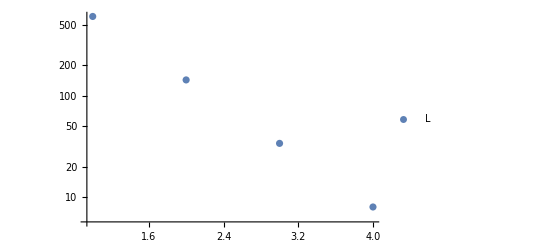

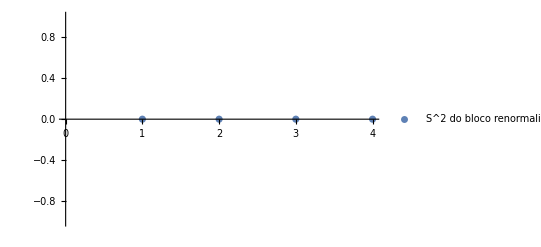

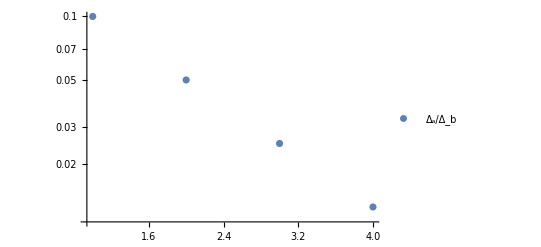

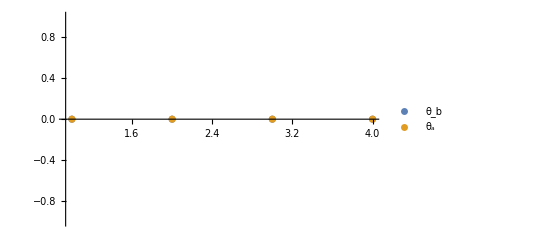

```mathematica
ListLogPlot[Dados⟦All,1⟧,PlotRange->All,PlotLegends->{"L"}]
ListPlot[Flatten[Spins],PlotLegends->{"S^2 do bloco renormalizado"}]
ListLogPlot[Dados⟦All,2⟧,PlotRange->All,PlotLegends->{"Δ_a/Δ_b"}]
ListPlot[{Dados⟦All,3⟧,Dados⟦All,4⟧},PlotRange->All,PlotLegends->{"θ_b","θ_a"}]
```

## Cadeia de Fib spin 1

```mathematica
num=Fibonacci[15];
Clear[cadeia];
Jb=1;
θ=50Degree;
{Kb1,Kb2}=N[JDtoK[Jb Cos[θ],Jb Sin[θ]]];
r=10;
cadeia[1]=Cadeiafibonacci[num-1,Kb1,Kb2,r];
{cadeia[2],spins[1],dados[1],fator[1],isborda[1]}=Renormalizar[cadeia[1]];
i=3;
Off[Eigenvalues::arh];
Off[Eigensystem::arh];
While[cadeia[i-1]!=cadeia[i-2],
{cadeia[i],spins[i-1],dados[i-1],fator[i-1],isborda[i-1]}=Renormalizar[cadeia[i-1]];
i++
];
j=1;
l=1;
While[j<i-3,If[Not[isborda[j]],{{data[l]=dados[j],sps[l]=spins[j][[1]]},l++,j++},j++]];
Dados=Array[data,l-1];
Spins=Array[sps,l-1];
Fator=Array[fator,i-3];
gap=gapcad[cadeia[i-1]]*Product[Fator[[i]],{i,1,Length[Fator]}];
Print["Inicial  "]; Imagemcadeia[cadeia[1][[1;;15]]]
Print["final  "]; Imagemcadeia[cadeia[i-1]]
Print["Gap final: ",N[gap,3]]
```

Inicial

-Graphics-

final

-Graphics-

Gap final: 0.0000333898

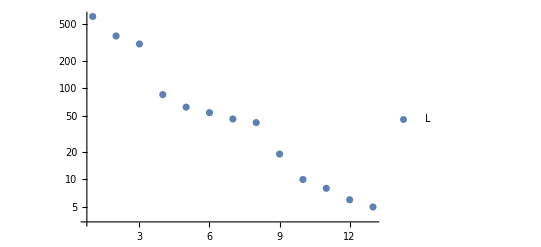

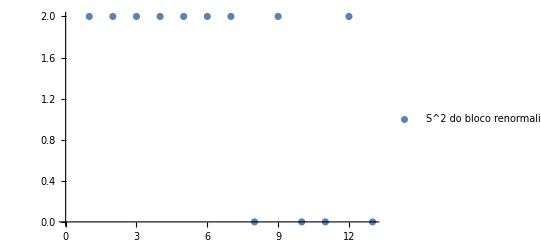

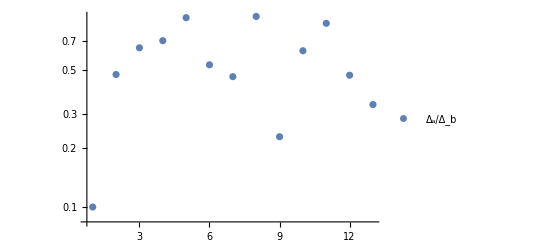

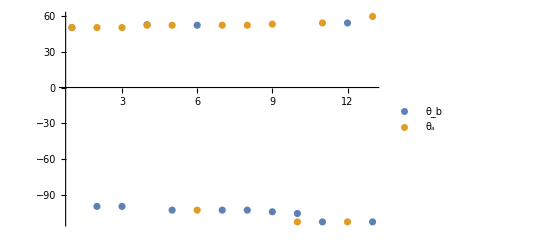

```mathematica
ListLogPlot[Dados⟦All,1⟧,PlotRange->All,PlotLegends->{"L"}]
ListPlot[Flatten[Spins],PlotLegends->{"S^2 do bloco renormalizado"}]
ListLogPlot[Dados⟦All,2⟧,PlotRange->All,PlotLegends->{"Δ_a/Δ_b"}]
ListPlot[{Dados⟦All,3⟧,Dados⟦All,4⟧},PlotRange->All,PlotLegends->{"θ_b","θ_a"}]
```

## Cadeia 63

```mathematica
num=Num63[5];
Clear[cadeia];
Jb=1;
θ=60Degree;
{Kb1,Kb2}=N[JDtoK[Jb Cos[θ],Jb Sin[θ]]];
r=10;
cadeia[1]=Cadeia36[num-1,Kb1,Kb2,r];
{cadeia[2],spins[1],dados[1],fator[1],isborda[1]}=Renormalizar[cadeia[1]];
i=3;
Off[Eigenvalues::arh]
Off[Eigensystem::arh]
While[cadeia[i-1]!=cadeia[i-2],
{cadeia[i],spins[i-1],dados[i-1],fator[i-1],isborda[i-1]}=Renormalizar[cadeia[i-1]];
i++
]
j=1;
l=1;
While[j<i-3,If[Not[isborda[j]],{{data[l]=dados[j],sps[l]=spins[j][[1]]},l++,j++},j++]];
Dados=Array[data,l-1];
Spins=Array[sps,l-1];
Fator=Array[fator,i-3];
gap=gapcad[cadeia[i-1]]*Product[Fator[[i]],{i,1,Length[Fator]}];
Print["Inicial  "]; Imagemcadeia[cadeia[1][[1;;15]]]
Print["final  "]; Imagemcadeia[cadeia[i-1]]
Print["Gap final: ",N[gap,3]]
```

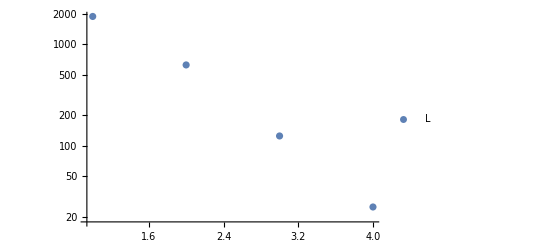

-Graphics-

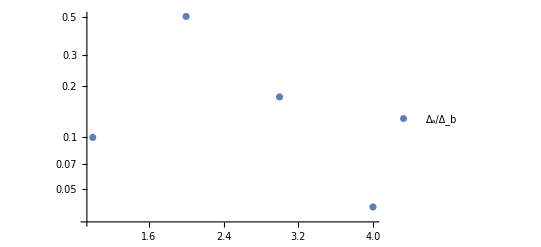

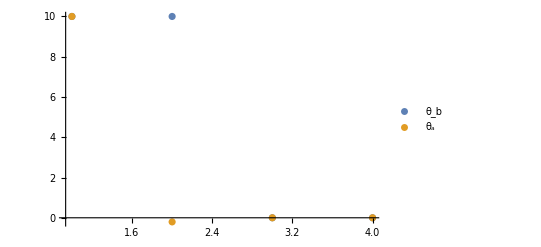

```mathematica
ListLogPlot[Dados⟦All,1⟧,PlotRange->All,PlotLegends->{"L"}]
ListPlot[Flatten[Spins],PlotLegends->{"S^2 do bloco renormalizado"}]
ListLogPlot[Dados⟦All,2⟧,PlotRange->All,PlotLegends->{"Δ_a/Δ_b"}]
ListPlot[{Dados⟦All,3⟧,Dados⟦All,4⟧},PlotRange->All,PlotLegends->{"θ_b","θ_a"}]
```

```mathematica
novaligacao[cadeia[3]][[1]]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]